```mathematica
import[file_]:=Module[{imp,toe,data,combined,lasts},
imp=Import["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data/"~~ToString@file];
toe=ToExpression/@StringSplit[imp];
data=Partition[toe,2];
combined=Gather[data,#1[[1]]==#2[[1]]&];
lasts={#[[1,1]],Max@#[[All,2]]}&/@combined;
{StringSplit[file,"-"][[1]],lasts}
]
```

```mathematica
SetDirectory["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data"]
```

/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data

```mathematica
data=import/@FileNames["*.txt"]
```

{{cache,{{1,7},{2,10},{3,22},{4,37},{5,213},{6,304},{7,753},{8,1310},{9,2583},{10,5240},{11,7966},{12,22010},{13,37586},{14,62466},{15,121499}}},{cache,{{1,4},{2,7},{3,19},{4,34},{5,274},{6,379},{7,1034},{8,1609},{9,3298},{10,7669},{11,10585},{12,14207},{13,29339},{14,76262},{15,96797},{16,120966}}},{cache,{{1,4},{2,7},{3,19},{4,35},{5,210},{6,301},{7,750},{8,1307},{9,3245},{10,6091},{11,12661},{12,22122},{13,45597},{14,80907},{15,111630},{16,119442}}},{cache,{{1,6},{2,9},{3,21},{4,37},{5,213},{6,304},{7,760},{8,1132},{9,3205},{10,4719},{11,10873},{12,22756},{13,32906},{14,40024},{15,70412},{16,111933},{17,119441}}},{irreversible,{{1,7},{2,14},{3,45},{4,88},{5,534},{6,812},{7,1345},{8,2978},{9,6440},{10,12179},{11,26877},{12,103593},{13,122505}}},{irreversible,{{1,7},{2,14},{3,45},{4,87},{5,533},{6,811},{7,1348},{8,2985},{9,7626},{10,16138},{11,54015},{12,105500},{13,114294},{14,122006}}},{irreversible,{{1,7},{2,13},{3,44},{4,87},{5,531},{6,808},{7,1339},{8,2947},{9,4668},{10,12756},{11,28884},{12,41984},{13,119435}}},{irreversible,{{1,7},{2,14},{3,46},{4,89},{5,536},{6,813},{7,1347},{8,2959},{9,4686},{10,12776},{11,27288},{12,58921},{13,109795},{14,119417}}},{naive,{{1,9},{2,16},{3,36},{4,71},{5,286},{6,428},{7,1450},{8,2285},{9,6454},{10,14484},{11,20761},{12,67361},{13,120661}}},{naive,{{1,11},{2,18},{3,38},{4,72},{5,284},{6,426},{7,1641},{8,2635},{9,7391},{10,13674},{11,37895},{12,69599},{13,122837}}},{naive,{{1,8},{2,15},{3,35},{4,69},{5,282},{6,424},{7,1452},{8,3372},{9,9904},{10,14572},{11,50286},{12,75063},{13,119406}}},{naive,{{1,9},{2,15},{3,35},{4,70},{5,284},{6,425},{7,1556},{8,2747},{9,6184},{10,16100},{11,34464},{12,99172},{13,105545},{14,119422}}},{stockfish,{{1,2},{2,2},{3,2},{4,2},{5,4},{6,6},{7,7},{8,9},{9,14},{10,22},{11,35},{12,47},{13,158},{14,280},{15,445},{16,669},{17,1103},{18,1714},{19,2526},{20,2861},{21,3685},{22,6791},{23,12959},{24,15692},{25,20371},{26,29526},{27,38528},{28,48625},{29,75677},{30,120004}}},{stockfish,{{1,1},{2,1},{3,1},{4,2},{5,3},{6,5},{7,7},{8,9},{9,14},{10,21},{11,35},{12,47},{13,158},{14,281},{15,446},{16,672},{17,1108},{18,1720},{19,2535},{20,2870},{21,3698},{22,6813},{23,12996},{24,15738},{25,20433},{26,29614},{27,38641},{28,48766},{29,75889},{30,119988}}},{stockfish,{{1,1},{2,1},{3,1},{4,2},{5,3},{6,5},{7,7},{8,9},{9,14},{10,21},{11,35},{12,47},{13,158},{14,281},{15,446},{16,672},{17,1107},{18,1720},{19,2534},{20,2870},{21,3697},{22,6812},{23,12999},{24,15739},{25,20431},{26,29610},{27,38638},{28,48763},{29,75894},{30,119987}}}}

```mathematica
medians=Gather[data,#1[[1]]==#2[[1]]&]//{#[[1,1]],Sequence@@#&/@#[[All,2,All]]}&/@#&//{#[[1]],{#[[1,1]],Median@#[[All,2]]}&/@Gather[#[[2]],#[[1]]==#2[[1]]&]}&/@#&
```

{{cache,{{1,5},{2,8},{3,20},{4,36},{5,213},{6,304},{7,1513/2},{8,2617/2},{9,3225},{10,11331/2},{11,10729},{12,22066},{13,35246},{14,69364},{15,208427/2},{16,119442},{17,119441}}},{irreversible,{{1,7},{2,14},{3,45},{4,175/2},{5,1067/2},{6,1623/2},{7,1346},{8,5937/2},{9,5563},{10,12766},{11,28086},{12,81257},{13,233729/2},{14,241423/2}}},{naive,{{1,9},{2,31/2},{3,71/2},{4,141/2},{5,284},{6,851/2},{7,1504},{8,2691},{9,13845/2},{10,14528},{11,72359/2},{12,72331},{13,240067/2},{14,119422}}},{stockfish,{{1,1},{2,1},{3,1},{4,2},{5,3},{6,5},{7,7},{8,9},{9,14},{10,21},{11,35},{12,47},{13,158},{14,281},{15,446},{16,672},{17,1107},{18,1720},{19,2534},{20,2870},{21,3697},{22,6812},{23,12996},{24,15738},{25,20431},{26,29610},{27,38638},{28,48763},{29,75889},{30,119988}}}}

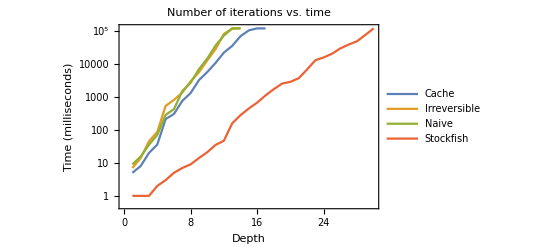

```mathematica
ttdGraph=Module[{d,cache,irreversible,naive,stockfish,legends,labels,lp,joined},
d=medians;
cache=Select[d,#[[1]]=="cache"&][[1,2]];
irreversible=Select[d,#[[1]]=="irreversible"&][[1,2]];
naive=Select[d,#[[1]]=="naive"&][[1,2]];
stockfish=Select[d,#[[1]]=="stockfish"&][[1,2]];

legends={"Cache","Irreversible","Naive","Stockfish"};
labels={"Depth","Time (milliseconds)"};
lp=ListLogPlot[{cache,irreversible,naive,stockfish},PlotLegends->legends,PlotLabel->"Number of iterations vs. time",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[1]];
joined=ListLogPlot[{cache,irreversible,naive,stockfish},PlotLegends->legends,FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[2]];
ListLogPlot[{cache,irreversible,naive,stockfish},PlotLegends->legends,PlotLabel->"Number of iterations vs. time",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True]
]
```

```mathematica
?MapThread
```

MapThread[f,{{a_1,a_2,…},{b_1,b_2,…},…}] gives {f[a_1,b_1,…],f[a_2,b_2,…],…}. 
MapThread[f,{expr_1,expr_2,…},n] applies f to the parts of the expr_i at level n.

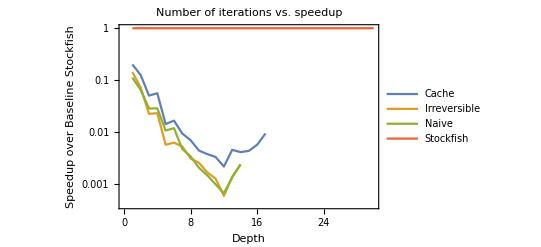

```mathematica
ttdSpeedupGraph=Module[{d,cache,irreversible,naive,stockfish,legends,labels,lp,joined,tS,speedup},
d=medians;
cache=Select[d,#[[1]]=="cache"&][[1,2]];
irreversible=Select[d,#[[1]]=="irreversible"&][[1,2]];
naive=Select[d,#[[1]]=="naive"&][[1,2]];
stockfish=Select[d,#[[1]]=="stockfish"&][[1,2]];
tS=stockfish[[All,2]];
speedup[data_]:=MapThread[{#[[1]],#2/#[[2]]}&,{data,tS[[;;Length@data]]}];

legends={"Cache","Irreversible","Naive","Stockfish"};
labels={"Depth","Speedup over Baseline Stockfish"};
lp=ListLogPlot[speedup/@{cache,irreversible,naive,stockfish},PlotLegends->legends,PlotLabel->"Number of iterations vs. speedup",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[1]];
joined=ListLogPlot[{cache,irreversible,naive,stockfish},PlotLegends->legends,FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[2]];
ListLogPlot[speedup/@{cache,irreversible,naive,stockfish},PlotLegends->legends,PlotLabel->"Number of iterations vs. speedup",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True]
]
```

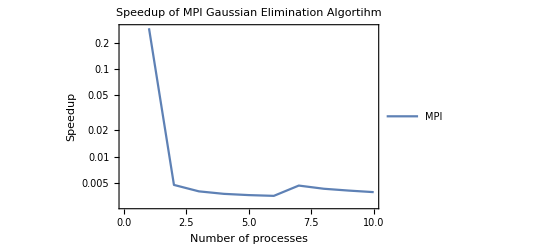

```mathematica
mpiSpeedupGraph=Module[{d,mpi,blocked,g,condense,seq2threads,legends,labels,lp,joined,tS,speedup},
d=mpiData[[All,;;3]];
blocked=ConstantArray[mpiData[[1]],10][[All,2;;]];
mpi=Select[d,#[[1]]=="mpi"&][[All,2;;]];
tS=mpi[[1,1]];
g[data_]:=Gather[data,#[[1]]==#2[[1]]&];
condense[data_]:={#[[1,1]],Median@#[[All,2]]}&/@g[data];
speedup[data_]:={#[[1]],tS/#[[2]]}&/@condense[data];

legends={"MPI"};
labels={"Number of processes","Speedup"};
lp=ListLogPlot[speedup/@{mpi,blocked},PlotLegends->legends,PlotLabel->"Speedup of MPI Gaussian Elimination Algortihm",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[1]];
joined=ListLogPlot[speedup/@{mpi,blocked},PlotLegends->legends,FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[2]];
Legended[lp,joined]
]
```

```mathematica
?StringContainsQ
```

```mathematica
Export["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/A4/plots/timeMPI.png",mpiGraph]
```

/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/A4/plots/timeMPI.png

```mathematica
Export["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/A4/plots/speedupMPI.png",mpiSpeedupGraph]
```

```mathematica
import[file_]:=Module[{out,err,nbytes,nm1,run},
out=Import["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/A4/histogram/data/"~~ToString@file~~".out"]//StringSplit[#,"\n"]&;
err=Import["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/A4/histogram/data/"~~ToString@file~~".err"]//StringSplit[#,"\n"]&;
nbytes=Select[err,StringContainsQ[#,"Number of bytes read"]&]//StringSplit[#[[1]],"="][[2]]&;
nm1=StringSplit@out[[-1]];
run=file//StringSplit[#,"_"][[1]]&//StringSplit[#,"run"][[1]]&//ToExpression;
{nm1[[1]],run,ToExpression@nbytes,ToExpression@nm1[[2]]}
]
```

```mathematica
"run10_gutenberg"//StringSplit[#,"_"][[1]]&//StringSplit[#,"run"][[1]]&//ToExpression
```

10

```mathematica
?ToExpression
```

ToExpression[input] gives the expression obtained by interpreting strings or boxes as Wolfram Language input. 
ToExpression[input,form] uses interpretation rules corresponding to the specified form. 
ToExpression[input,form,h] wraps the head h around the expression produced before evaluating it.

```mathematica
SetDirectory["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/A4/histogram/data"]
```

/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/A4/histogram/data

```mathematica
fnames=FileNames["*.out"]//StringSplit[#,".out"][[1]]&/@#&
```

{run10_gutenberg,run10_large,run10_medium,run10_small,run1_gutenberg,run1_large,run1_medium,run1_small,run2_gutenberg,run2_large,run2_medium,run2_small,run3_gutenberg,run3_large,run3_medium,run3_small,run4_gutenberg,run4_large,run4_medium,run4_small,run5_gutenberg,run5_large,run5_medium,run5_small,run6_gutenberg,run6_large,run6_medium,run6_small,run7_gutenberg,run7_large,run7_medium,run7_small,run8_gutenberg,run8_large,run8_medium,run8_small,run9_gutenberg,run9_large,run9_medium,run9_small}

```mathematica
hadoopData=import/@fnames
```

{{gutenberg,10,27053656,21318},{large,10,11677702770,295607},{medium,10,4275626000,121326},{small,10,46,16381},{gutenberg,1,27053656,20693},{large,1,11679299050,300270},{medium,1,4275626000,119110},{small,1,46,16952},{gutenberg,2,27053656,21867},{large,2,11679299050,295899},{medium,2,4275626000,116044},{small,2,46,17068},{gutenberg,3,27053656,21235},{large,3,11679299050,302208},{medium,3,4275626000,118250},{small,3,46,15725},{gutenberg,4,27053656,20571},{large,4,11679299050,311083},{medium,4,4275626000,118891},{small,4,46,15643},{gutenberg,5,27053656,22534},{large,5,11679299050,300628},{medium,5,4275626000,122754},{small,5,46,17201},{gutenberg,6,27053656,20630},{large,6,11658744570,316027},{medium,6,4275626000,124781},{small,6,46,15601},{gutenberg,7,27053656,20903},{large,7,11673806340,416323},{medium,7,4275626000,131894},{small,7,46,16070},{gutenberg,8,27053656,23432},{large,8,11679299050,291698},{medium,8,4275626000,124658},{small,8,46,27784},{gutenberg,9,27053656,29797},{large,9,11679299050,291722},{medium,9,4275626000,143492},{small,9,46,15830}}

15.4968+2.7049×10^-8 x

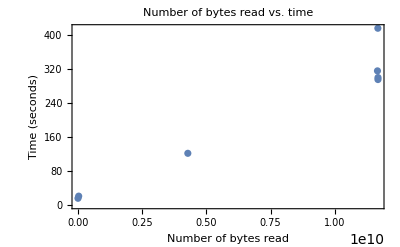

```mathematica
hadoopVariability=Module[{d,g,condense,legends,labels,lp,joined,tS,line},
d=hadoopData;
g[data_]:=Gather[data,#[[3]]==#2[[3]]&];
condense[data_]:={#[[1,3]],Median@(#[[All,4]]/1000)}&/@g[data];
line[data_]:=Fit[data, {1,x},x];
Print@line[condense@d];
legends={"Number of bytes read vs. time"};
labels={"Number of bytes read","Time (seconds)"};
lp=condense@d//Show[ListPlot[#,PlotLabel->legends[[1]],FrameLabel->labels,Frame->{{True,False},{True,False}}],Plot[line,{x,0,3*10^10}]]&
]
```

```mathematica
Export["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/A4/plots/hadoop.png",hadoopVariability]
```

/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/A4/plots/hadoop.png